## Subradiance-protected excitation spreading for collimated photon emission

P. Huft
See paper by K. Ballantine, J. Ruostekoski

## personal notes

### Questions

Why can a system which is excited with a single photon be adequately described by classical E&M?

The collective mode which is predominantly coupled by the initial excitation (after rotating the polarization to be normal to the atom grid plane) decays slowly, i.e. is subradiant, while other modes decay superradiantly. Why do these other modes see an a higher rate of decay than independent decay? Does it just “come out of the math” as with the √N enhancement of ensemble Rabi flopping?

## setup

System description: atomnum two-level atoms arranged in a 2D square grid with equal periodicity in x and y. The lower level is has only one angular momentum state (J=0) while the upper state has three Zeeman sublevels (J=1).

```mathematica
(*PHYSICAL CONSTANTS*)
ℏ = 6.62607015*^-34/(2π);
μ0 =4π*10^-7;
c = 299792458;
ϵ0 = 1/(c^2 μ0);
ee = 1.602*^-19; (*electron charge*)
a0 = 5.27*^-11; (*Bohr radius*)
(*PARAMETERS and other DEFINITIONS*)
atomnum = 5*5; (*should be an odd perfect square*)
J = 1; (*upper level total angular momentum*) 
λ = 7.8*10^-7;
k =2π/λ;
matelem = ee a0; (*just assume a general matrix element is of this order for now.*)
γ = matelem^2 k^3/(6 π ℏ ϵ0); (*single two-level atom linewidth*)
a=0.75 λ; (*atomic grid spatial period*)
pol = Range[3];(*pol[[μ]]/.u->1,2,3 for polarization σ=-1,0,+1 *)
Subscript[Δ, μ_]:= {0,0,0}[[μ]]; (*no Zeeman splitting for now*)
deg = 2J+1;
dim = deg*atomnum; (*Hamiltonian shape is dim x dim, with state vector = dim*)
(*get 1D atom idx from 2D coordinate indices*)
(*FUNCTIONS*)
idx[i_,j_,n_]:=(i-1)n+j//Simplify; 
Subscript[r, i_,j_]:={Mod[j-1,n]-Mod[i-1,n],Floor[(j-1)/n]-Floor[(i-1)/n]}/.n->atomnum;(*distance between atoms i,j in units lattice spacing*)
sphrWave[x_,y_,z_]:=(ⅇ^(ⅈ k √(x^2+y^2+z^2)))/(4 π √(x^2+y^2+z^2));(*spherical wave*)
Subscript[Kδ, μ_,ν_]:=KroneckerDelta[SymbolName[μ],SymbolName[ν]];(*symbolic Kronecker delta*)
dipOp[α_,β_]=(D[#,α]D[#,β]-Subscript[Kδ, α,β] Laplacian[#,{x,y,z}]-Subscript[Kδ, α,β] DiracDelta[√(x^2+y^2+z^2)])&; (*derivative op in the expression for positive freq. component of monochromatic dipole radation*)
Subscript[G, α_,β_]:=dipOp[α,β][sphrWave[x,y,z]];(*element (α,β) of the positive frequency compenent of monochromatic dip. radiation*)
GTensor = Table[Subscript[G, α,β]+(Subscript[Kδ, α,β] DiracDelta[√(x^2+y^2+z^2)])/3,{α,{x,y,z}},{β,{x,y,z}}];
Subscript[e, μ_] :={{1,0,0},{0,1,0},{0,0,1}}[[μ]]; (*{1/(√2){1,-ⅈ 1,0},{0,0,1},1/(√2){1,ⅈ 1,0}}[[μ]];*)
(*polar polarization basis. μ=1,2,3 -> polarization σ=-1,0,+1 or x,y,z*)
GTensorElem = Table[Subscript[e, n]*.GTensor.Subscript[e, m],{n,Range[3]},{m,Range[3]}]; (*GTensor in spherical basis*)
Subscript[dipRadKernel, μ_,ν_,i_,j_,a_]:= Module[{u=a Subscript[r, i,j],v,Ω,γ},
(*returns Re,Im parts of the dipole radiation kernel between atoms i,j in polarization states μ,ν. I have manually removed the Kronecker delta in this definition as we should never be concerned with cases in which atoms overlap*)
v= GTensorElem[[μ,ν]]/.z->0 //ComplexExpand;
Ω = If[i==j,0,Re[v/.{x-> u[[1]],y-> u[[2]]}]];(*returns zero for i==j because Subscript[Ω, ij] is only defined for coupling between different atoms*)
γ = If[i==j,0(*Limit[Limit[Im[v],x-> u[[1]]],y-> u[[2]]]*),Im[v/.{x-> u[[1]],y-> u[[2]]}]];
(*use 0 for i=j when using Cartesian basis*)
{Ω,γ}
]
```

Restricting this problem to the single-excitation subspace, the Hamiltonian matrix elements are: H_(3j-1+ν,3k-1+ν)=H_νμ^(jk)=Δ_μ δ_jk δ_μν+Ω_μν^(jk)(1-δ_jk)+ⅈ γ_μν^(jk), where μ,ν specify polarization in a spherical basis and j,k are the atom indices in the 2D grid. The dynamics in this subspace are coherent, but H is non-Hermitian, so there is dissipation as the excitation diffuses into the collective ground state.

- Δ,γ values used are arbitrary with the given choice of plot units.

## run

This fills the Hamiltonian without errors, but many of the elements are large. perhaps there is a better choice of units to help avoid overflow issues when running the calculation

```mathematica
(*initialize the state vector. excite central 9 atoms in m=0 states*)

state = Array[Subscript[b, ##]&,dim];
excitedIdcs = Flatten@Table[(deg*atomnum-1)/2+deg*√atomnum i+deg j-1,{i,{-1,0,1}},{j,{-1,0,1}}];
state[[excitedIdcs]]=1; 
ipstate = Array[KroneckerDelta[2,Mod[#,2 J+1]]&,dim];(*in-plane state: each atom excited with P=y*)
afstate= Array[(-1)^# KroneckerDelta[1,Mod[#,2 J+1]]&,dim];(*antiferromagnetic state: every atom has P=x, but alternating phases*)
fstate = Array[KroneckerDelta[0,Mod[#,2 J+1]]&,dim];(*ferromagnetic state: each atom excited with P=x, all in phase*)
statelist = {{ipstate,"In-plane"},{fstate,"Ferromagnetic"},{fstate,"Antiferromagnetic"}};
soln=Array[{}&,Length[statelist]];
```

```mathematica
(*afstate[[1;;15]]*)
```

{1,0,0,0,0,1,1,0,0,0,0,1,1,0,0}

```mathematica
(*calculate the collective linewidths for statelist modes as a function of lattice spacing*)
(*until i include more modes: {d,Log10[Subscript[γ, n]/γ]}*)
For[d=0.025,d<1.2,d=d+0.025,(*loop over fractional lattice period*)
(*build the Hamiltonian*)
Hfull = Array[Subscript[H, ##]&,{dim,dim}];
For[i=1,i<atomnum+1,i++,
For[j=1,j<atomnum+1,j++,
For[ν=1,ν<deg+1,ν++,
For[μ=1,μ<deg+1,μ++,
period = d λ;
G = Subscript[dipRadKernel, μ,ν,i,j,period]; 
Ωμνij=(6 π γ)/k^3 G[[1]];
γμνij =(6 π γ)/k^3 G[[2]];
Hfull[[3(i-1)+ν,3(j-1)+μ]]= Subscript[Δ, μ] KroneckerDelta[i,j]KroneckerDelta[μ,ν]+Ωμνij(1-KroneckerDelta[i,j])+ⅈ γμνij;
];
];
];
];
(*find the linewidth of mode which most nearly overlaps the state vector of interest*)
Clear[evals,evecs];
{evals,evecs} = Eigensystem[Hfull];
For[sidx=1,sidx<Length[statelist]+1,sidx++,
overlap = {};(*list with entries {idx, overlap coefficient}*)
For[i = 1,i<Length[evecs]+1,i++,
AppendTo[overlap,{i,Abs[fstate.evecs[[i]]]}]
];
maxIdx=Sort[overlap,#1[[2]]>#2[[2]]&][[1,1]];
AppendTo[soln[[sidx]],{d,Log10[Im[evals[[maxIdx]]]/γ]}];
];
];
```

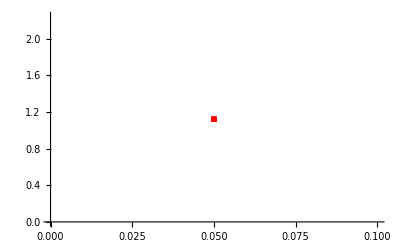

```mathematica
markers = {Graphics[{Blue, Disk[]}],Graphics[{Red,Rectangle[]}],Graphics[{Green, Disk[]}]};
plots = {};
For[lidx=1,lidx<Length[soln]+1,lidx++,
AppendTo[plots,ListPlot[soln[[lidx]],PlotLegends->statelist[[lidx,2]],PlotMarkers->{markers[[lidx]],0.02}]];
]
Show[plots]
```

## tests

made a mistake in my polarization basis-- should be cartesian for now. no zeeman splitting, and ferro/anti-ferro states have x polarizations. Now i get infinite elements of my hamiltonian though, so time to diagnose

```mathematica
period = 0.5 λ;
μ=2;ν=2;i=1;j=1;
G = Subscript[dipRadKernel, μ,ν,i,j,period]; 
Ωμνij=(6 π γ)/k^3 G[[1]];
γμνij =(6 π γ)/k^3 G[[2]];
Hfull[[3(i-1)+ν,3(j-1)+μ]]= Subscript[Δ, μ] KroneckerDelta[i,j]KroneckerDelta[μ,ν]+Ωμνij(1-KroneckerDelta[i,j])+ⅈ γμνij
```

ⅈ ∞

```mathematica
(*Find the basis eigenvalues of interest by diagonalizing the Hamiltonian and then finding the overlap of the resultant e-vecs with the desired basis vectors*)
{evals,evecs} = Eigensystem[Hfull];
```

```mathematica
fstate = Array[KroneckerDelta[2,Mod[#,2 J+1]]&,dim];(*ferromagnetic state: each atom excited with m=0*)
(*afstate = Array[KroneckerDelta[,Mod[#,2(2J+1)]]]*)
```

```mathematica
{evals,evecs} = Eigensystem[Hfull];
overlap = {};(*list with entries {idx, overlap coefficient}*)
For[i = 1,i<Length[evecs]+1,i++,
AppendTo[overlap,{i,Abs[fstate.evecs[[i]]]}]
]
maxIdx=Sort[overlap,#1[[2]]>#2[[2]]&][[1,1]];
linewidth=Log10[Im[evals[[maxIdx]]]/γ];
```

7.33422

```mathematica
period
```

1.05

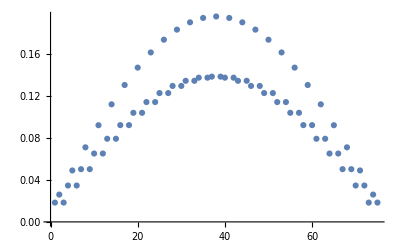

```mathematica
ListPlot[Re[evecs[[maxIdx]]]]
```

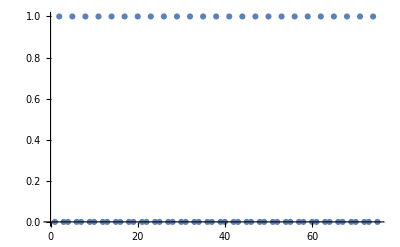

```mathematica
ListPlot[fstate]
```

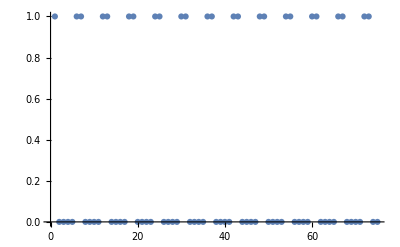

```mathematica
ListPlot[afstate]
```

```mathematica
fstate = Array[KroneckerDelta[2,Mod[#,3]]&,dim];(*anti-ferromagnetic state*)
```

```mathematica
afstate= Array[Boole[(u==1|| u==0)/.u-> Mod[#,6]]&,15]
```

{1,0,0,0,0,1,1,0,0,0,0,1,1,0,0}

```mathematica
Array[Boole[(u==1|| u==0)/.u-> Mod[#,6]]&,12]
```

{1,0,0,0,0,1,1,0,0,0,0,1}

```mathematica
1,2,3,4,5,6,7,8,9,10,11,12,13,14,15
1,0,0,0,0,1,1,0,0,0,0,1,1,0,0
```

every other group of three, use KroneckerDelta[1or2,Mod[#,3]]] to set value to 1.

Build anti/ferromag. states, and then calculate overlap with a given basis vector list

```mathematica
fstate = Array[KroneckerDelta[2,Mod[#,3]]&,9]
```

```mathematica
%
```

{299792458,599584916,899377374,1199169832,1498962290,1798754748,2098547206,2398339664,2698132122}

Check my grid mapping. 2D grid, but only one index to specify atoms

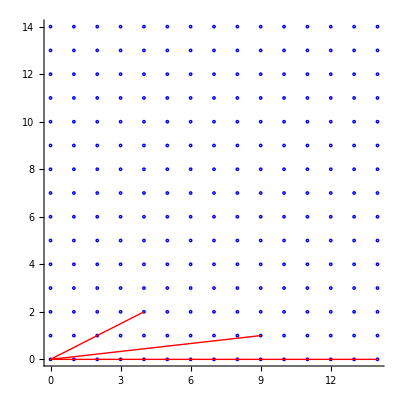

```mathematica
num=atomnum;
a=1;(*0.7;*)
r[i_,j_] :=Graphics[{Red,Line[{a{Mod[i-1,num], Floor[(i-1)/num]},a{Mod[j-1,num],Floor[(j-1)/num]}}]}];
Show[Table[Graphics[{Blue,Circle[a{Mod[i-1,num],Floor[(i-1)/num]},0.05]}],{i,Range[num^2]}],Table[r[1,j],{j,{15,25,35}}],(*PlotLegends-> Placed[{"hi"},{1/(a num)//N,1/(a num)//N}],*) Axes->True,PlotRange->{{0,a (num-1)},{0,(a num-1)}}]
```

What 1D atom idx corresponds to (i,j)?

```mathematica
idx[i_,j_,n_]:=(i-1)n+j//Simplify;
```

```mathematica
idx[2,2,n]
```

2+n

```mathematica
idx[1,1,n]//Simplify
```

(2+n)/2

```mathematica
Solve[{n+2== 2 (α  + β),n==α +β n },{α,β} ]
```

{{α→n^2/(2 (-1+n)),β→-(2-n)/(2 (-1+n))}}

```mathematica
Clear[i,j]
```

```mathematica
{Mod[i-1,num],Floor[(i-1)/num]}/.{i-> 2,j-> 2}
```

{1,0}

```mathematica
1/(a num)//N
```

0.0666667

```mathematica
Legended
```

```mathematica
r[i_,j_] :=a{Mod[j-1,num]-Mod[i-1,num],Floor[(j-1)/num]-Floor[(i-1)/num]};
```

```mathematica
r[1,15]
```

{2.8,1.4}

```mathematica
υ = Table[x^2+y^2,{x,{-1,0,1}},{y,{-1,0,1}}]
```

{{2,1,2},{1,0,1},{2,1,2}}

```mathematica
{1,0,1}.υ
```

{4,2,4}